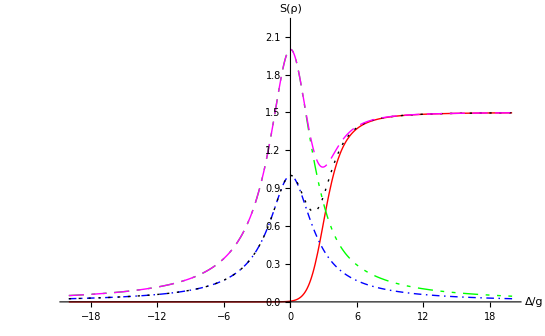

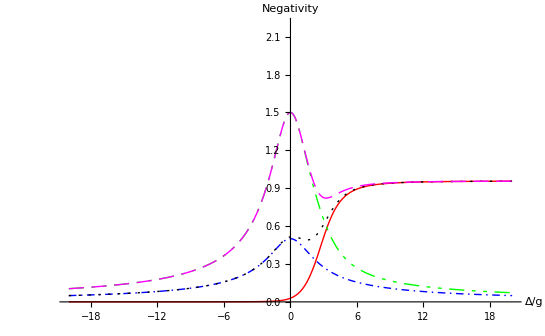

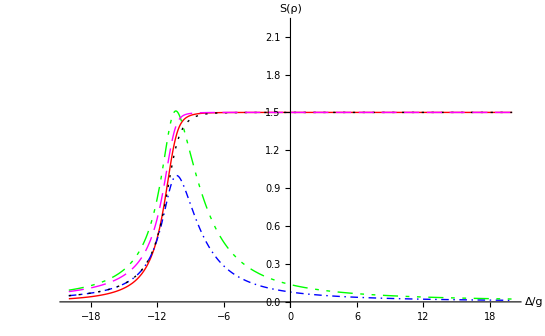

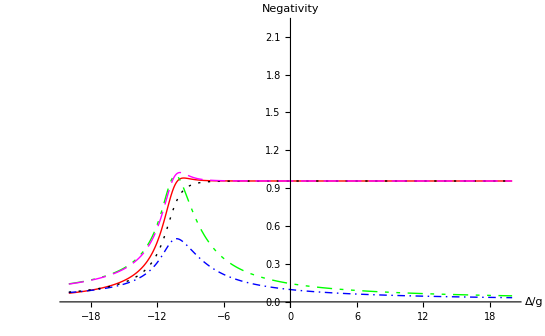

```mathematica
SuperDagger[a_]:=Transpose[Conjugate[a]] 
x_⊗y_:=Table[x[[Floor[(i-1)/(Dimensions[y][[1]])+1],Floor[(j-1)/(Dimensions[y][[2]])+1]]]*y[[Mod[i-1,Dimensions[y][[1]]]+1,Mod[j-1,Dimensions[y][[2]]]+1]],{i,1,Dimensions[x][[1]]*Dimensions[y][[1]],1},{j,1,Dimensions[x][[2]]*Dimensions[y][[2]],1}]

ClearAll[x,wc,wa,g,A,H]
n0=({{1}, {0}, {0}});n1=({{0}, {1}, {0}});n2=({{0}, {0}, {1}});

a1=(n0.SuperDagger[n1]+√2 n1.SuperDagger[n2])⊗IdentityMatrix[12];
a2=IdentityMatrix[6]⊗((n0.SuperDagger[n1]+√2 n1.SuperDagger[n2])⊗IdentityMatrix[2]);
σ1=(IdentityMatrix[3]⊗({{0, 1}, {0, 0}}))⊗IdentityMatrix[6];
σ2=IdentityMatrix[18]⊗({{0, 1}, {0, 0}});
H=wc (SuperDagger[a1].a1+SuperDagger[a2].a2)+wa (SuperDagger[σ1].σ1+SuperDagger[σ2].σ2)+g (SuperDagger[a1].σ1+a1.SuperDagger[σ1]+SuperDagger[a2].σ2+a2.SuperDagger[σ2])+A (SuperDagger[a1].a2+SuperDagger[a2].a1);


n4=SuperDagger[a1].a1+SuperDagger[a2].a2+SuperDagger[σ1].σ1+SuperDagger[σ2].σ2;
ts=Table[0,{i,1,36}];
For[i1=0;k=0,i1≤2,,For[i2=0,i2≤1,,For[i3=0,i3≤2,,For[i4=0,i4≤1,,k=k+1;ts[[k]]={i1,i2,i3,i4};i4++];i3++];i2++];i1++]

ws=Table[0,{i,1,6}];
For[i1=0;k=0,i1≤2,,For[i2=0,i2≤1,,k=k+1;ws[[k]]={i1,i2};i2++];i1++]

t1[s0_]:=Module[{s12,i,j},s12=Table[0,{i,1,6},{j,1,6}];For[i=1,i≤36,,For[j=1,j≤36,,If[ts[[i]][[3]]==ts[[j]][[3]]&&ts[[i]][[4]]==ts[[j]][[4]],s12[[2ts[[i]][[1]]+ts[[i]][[2]]+1,2ts[[j]][[1]]+ts[[j]][[2]]+1]]=s12[[2ts[[i]][[1]]+ts[[i]][[2]]+1,2ts[[j]][[1]]+ts[[j]][[2]]+1]]+s0[[i,j]]];j++];i++];Return[s12]]

t2[s0_]:=Module[{s12,s2,i,j},s2=Table[0,{i,1,2},{j,1,2}];s12=t1[s0];For[i=1,i≤6,,For[j=1,j≤6,,If[ws[[i]][[1]]==ws[[j]][[1]],s2[[ws[[i]][[2]]+1,ws[[j]][[2]]+1]]=s2[[ws[[i]][[2]]+1,ws[[j]][[2]]+1]]+s12[[i,j]]];j++];i++];Return[s2]]

t3[s0_]:=Module[{s12,s1,i,j},s1=Table[0,{i,1,3},{j,1,3}];s12=t1[s0];For[i=1,i≤6,,For[j=1,j≤6,,If[ws[[i]][[2]]==ws[[j]][[2]],s1[[ws[[i]][[1]]+1,ws[[j]][[1]]+1]]=s1[[ws[[i]][[1]]+1,ws[[j]][[1]]+1]]+s12[[i,j]]];j++];i++];Return[s1]]

t4[s0_]:=Module[{s12,i,j},s12=Table[0,{i,1,4},{j,1,4}];For[i=1,i≤36,,For[j=1,j≤36,,If[ts[[i]][[1]]==ts[[j]][[1]]&&ts[[i]][[3]]==ts[[j]][[3]],s12[[2ts[[i]][[2]]+ts[[i]][[4]]+1,2ts[[j]][[2]]+ts[[j]][[4]]+1]]=s12[[2ts[[i]][[2]]+ts[[i]][[4]]+1,2ts[[j]][[2]]+ts[[j]][[4]]+1]]+s0[[i,j]]];j++];i++];Return[s12]]

t5[s0_]:=Module[{s12,i,j},s12=Table[0,{i,1,6},{j,1,6}];For[i=1,i≤36,,For[j=1,j≤36,,If[ts[[i]][[2]]==ts[[j]][[2]]&&ts[[i]][[3]]==ts[[j]][[3]],s12[[2ts[[i]][[1]]+ts[[i]][[4]]+1,2ts[[j]][[1]]+ts[[j]][[4]]+1]]=s12[[2ts[[i]][[1]]+ts[[i]][[4]]+1,2ts[[j]][[1]]+ts[[j]][[4]]+1]]+s0[[i,j]]];j++];i++];Return[s12]]
      t6[s0_]:=Module[{s12,i,j},s12=s0;For[i=1,i≤36,,For[j=1,j≤36,,If[ts[[i]][[3]]≠ts[[j]][[3]]||ts[[i]][[4]]≠ts[[j]][[4 ]],s12[[i,j]]=s0[[6(2ts[[i]][[1]]+ts[[i]][[2]])+2ts[[j]][[3]]+ts[[j]][[4]]+1,6(2ts[[j]][[1]]+ts[[j]][[2]])+2ts[[i]][[3]]+ts[[i]][[4]]+1]]];j++];i++];Return[s12]]

      t71[s0_]:=Module[{s12,i,j},s12=s0;For[i=1,i≤36,,For[j=1,j≤36,,If[ts[[i]][[2]]≠ts[[j]][[2]],s12[[i,j]]=s0[[6(2ts[[i]][[1]]+ts[[j]][[2]])+2ts[[i]][[3]]+ts[[i]][[4]]+1,6(2ts[[j]][[1]]+ts[[i]][[2]])+2ts[[j]][[3]]+ts[[j]][[4]]+1]]];j++];i++];Return[s12]]

      t72[s0_]:=Module[{s12,i,j},s12=s0;For[i=1,i≤36,,For[j=1,j≤36,,If[ts[[i]][[1]]≠ts[[j]][[1]]||ts[[i]][[3]]≠ts[[j]][[3]]||ts[[i]][[4]]≠ts[[j]][[4 ]],s12[[i,j]]=s0[[6(2ts[[j]][[1]]+ts[[i]][[2]])+2ts[[j]][[3]]+ts[[j]][[4]]+1,6(2ts[[i]][[1]]+ts[[j]][[2]])+2ts[[i]][[3]]+ts[[i]][[4]]+1]]];j++];i++];Return[s12]]


  t81[s0_]:=Module[{s12,i,j},s12=s0;For[i=1,i≤36,,For[j=1,j≤36,,If[ts[[i]][[1]]≠ts[[j]][[1]],s12[[i,j]]=s0[[6(2ts[[j]][[1]]+ts[[i]][[2]])+2ts[[i]][[3]]+ts[[i]][[4]]+1,6(2ts[[i]][[1]]+ts[[j]][[2]])+2ts[[j]][[3]]+ts[[j]][[4]]+1]]];j++];i++];Return[s12]]

  t82[s0_]:=Module[{s12,i,j},s12=s0;For[i=1,i≤36,,For[j=1,j≤36,,If[ts[[i]][[2]]≠ts[[j]][[2]]||ts[[i]][[3]]≠ts[[j]][[3]]||ts[[i]][[4]]≠ts[[j]][[4 ]],s12[[i,j]]=s0[[6(2ts[[i]][[1]]+ts[[j]][[2]])+2ts[[j]][[3]]+ts[[j]][[4]]+1,6(2ts[[j]][[1]]+ts[[i]][[2]])+2ts[[i]][[3]]+ts[[i]][[4]]+1]]];j++];i++];Return[s12]]

  t9[s0_]:=Module[{s12,i,j},s12=s0;For[i=1,i≤36,,For[j=1,j≤36,,If[ts[[i]][[1]]≠ts[[j]][[1]]||ts[[i]][[3]]≠ts[[j]][[3 ]],s12[[i,j]]=s0[[6(2ts[[j]][[1]]+ts[[i]][[2]])+2ts[[j]][[3]]+ts[[i]][[4]]+1,6(2ts[[i]][[1]]+ts[[j]][[2]])+2ts[[i]][[3]]+ts[[j]][[4]]+1]]];j++];i++];Return[s12]]

  t10[s0_]:=Module[{s12,i,j},s12=s0;For[i=1,i≤36,,For[j=1,j≤36,,If[ts[[i]][[2]]≠ts[[j]][[2]]||ts[[i]][[3]]≠ts[[j]][[3 ]],s12[[i,j]]=s0[[6(2ts[[i]][[1]]+ts[[j]][[2]])+2ts[[j]][[3]]+ts[[i]][[4]]+1,6(2ts[[j]][[1]]+ts[[i]][[2]])+2ts[[i]][[3]]+ts[[j]][[4]]+1]]];j++];i++];Return[s12]]




f12[ag_,dg_]:=Module[{vh,fh,nvh,i,t12,sq1},bx0=400;
g=1.0;A=ag*g;Δ=dg*g;wa=(bx0+Δ)/2;wc=(bx0-Δ)/2;
vh=Eigensystem[H];
fh=10^30;For[i=1,i≤36,,nvh=vh[[2,i]]/Norm[vh[[2,i]]];If[fh>vh[[1,i]]&&({nvh}.n4.Table[{Conjugate[nvh[[i]]]},{i,1,36}])[[1,1]]==2,fh=vh[[1,i]];p0=i];i++];
nvh=vh[[2,p0]]/Norm[vh[[2,p0]]];
(t12=t1[Table[{Conjugate[nvh[[i]]]},{i,1,36}].{nvh}]);
(sq1=Eigenvalues[t12]);Return[
-∑_(i=1)^Length[sq1] Limit[y0*Log[2,y0],y0->sq1[[i]]]//Chop]]

f2[ag_,dg_]:=Module[{vh,fh,nvh,i,t12,sq1},bx0=400;
g=1.0;A=ag*g;Δ=dg*g;wa=(bx0+Δ)/2;wc=(bx0-Δ)/2;
vh=Eigensystem[H];
fh=10^30;For[i=1,i≤36,,nvh=vh[[2,i]]/Norm[vh[[2,i]]];If[fh>vh[[1,i]]&&({nvh}.n4.Table[{Conjugate[nvh[[i]]]},{i,1,36}])[[1,1]]==2,fh=vh[[1,i]];p0=i];i++];
nvh=vh[[2,p0]]/Norm[vh[[2,p0]]];
(t12=t2[Table[{Conjugate[nvh[[i]]]},{i,1,36}].{nvh}]);
(sq1=Eigenvalues[t12]);Return[
-∑_(i=1)^Length[sq1] Limit[y0*Log[2,y0],y0->sq1[[i]]]//Chop]]

f1[ag_,dg_]:=Module[{vh,fh,nvh,i,t12,sq1},bx0=400;
g=1.0;A=ag*g;Δ=dg*g;wa=(bx0+Δ)/2;wc=(bx0-Δ)/2;
vh=Eigensystem[H];
fh=10^30;For[i=1,i≤36,,nvh=vh[[2,i]]/Norm[vh[[2,i]]];If[fh>vh[[1,i]]&&({nvh}.n4.Table[{Conjugate[nvh[[i]]]},{i,1,36}])[[1,1]]==2,fh=vh[[1,i]];p0=i];i++];
nvh=vh[[2,p0]]/Norm[vh[[2,p0]]];
(t12=t3[Table[{Conjugate[nvh[[i]]]},{i,1,36}].{nvh}]);
(sq1=Eigenvalues[t12]);Return[
-∑_(i=1)^Length[sq1] Limit[y0*Log[2,y0],y0->sq1[[i]]]//Chop]]

f24[ag_,dg_]:=Module[{vh,fh,nvh,i,t12,sq1},bx0=400;
g=1.0;A=ag*g;Δ=dg*g;wa=(bx0+Δ)/2;wc=(bx0-Δ)/2;
vh=Eigensystem[H];
fh=10^30;For[i=1,i≤36,,nvh=vh[[2,i]]/Norm[vh[[2,i]]];If[fh>vh[[1,i]]&&({nvh}.n4.Table[{Conjugate[nvh[[i]]]},{i,1,36}])[[1,1]]==2,fh=vh[[1,i]];p0=i];i++];
nvh=vh[[2,p0]]/Norm[vh[[2,p0]]];
(t12=t4[Table[{Conjugate[nvh[[i]]]},{i,1,36}].{nvh}]);
(sq1=Eigenvalues[t12]);Return[
-∑_(i=1)^Length[sq1] Limit[y0*Log[2,y0],y0->sq1[[i]]]//Chop]]

f14[ag_,dg_]:=Module[{vh,fh,nvh,i,t12,sq1},bx0=400;
g=1.0;A=ag*g;Δ=dg*g;wa=(bx0+Δ)/2;wc=(bx0-Δ)/2;
vh=Eigensystem[H];
fh=10^30;For[i=1,i≤36,,nvh=vh[[2,i]]/Norm[vh[[2,i]]];If[fh>vh[[1,i]]&&({nvh}.n4.Table[{Conjugate[nvh[[i]]]},{i,1,36}])[[1,1]]==2,fh=vh[[1,i]];p0=i];i++];
nvh=vh[[2,p0]]/Norm[vh[[2,p0]]];
(t12=t5[Table[{Conjugate[nvh[[i]]]},{i,1,36}].{nvh}]);
(sq1=Eigenvalues[t12]);Return[
-∑_(i=1)^Length[sq1] Limit[y0*Log[2,y0],y0->sq1[[i]]]//Chop]]

h12[ag_,dg_]:=Module[{vh,fh,nvh,i,t12,sq1},bx0=400;
g=1.0;A=ag*g;Δ=dg*g;wa=(bx0+Δ)/2;wc=(bx0-Δ)/2;
vh=Eigensystem[H];
fh=10^30;For[i=1,i≤36,,nvh=vh[[2,i]]/Norm[vh[[2,i]]];If[fh>vh[[1,i]]&&({nvh}.n4.Table[{Conjugate[nvh[[i]]]},{i,1,36}])[[1,1]]==2,fh=vh[[1,i]];p0=i];i++];
nvh=vh[[2,p0]]/Norm[vh[[2,p0]]];
(t12=t6[Table[{Conjugate[nvh[[i]]]},{i,1,36}].{nvh}]);
(sq1=Eigenvalues[t12]);Return[∑_(i=1)^Length[sq1] (Abs[sq1[[i]]]-sq1[[i]])/2]]

h21[ag_,dg_]:=Module[{vh,fh,nvh,i,t12,sq1},bx0=400;
g=1.0;A=ag*g;Δ=dg*g;wa=(bx0+Δ)/2;wc=(bx0-Δ)/2;
vh=Eigensystem[H];
fh=10^30;For[i=1,i≤36,,nvh=vh[[2,i]]/Norm[vh[[2,i]]];If[fh>vh[[1,i]]&&({nvh}.n4.Table[{Conjugate[nvh[[i]]]},{i,1,36}])[[1,1]]==2,fh=vh[[1,i]];p0=i];i++];
nvh=vh[[2,p0]]/Norm[vh[[2,p0]]];
(t12=t71[Table[{Conjugate[nvh[[i]]]},{i,1,36}].{nvh}]);
(sq1=Eigenvalues[t12]);Return[∑_(i=1)^Length[sq1] (Abs[sq1[[i]]]-sq1[[i]])/2]]

h22[ag_,dg_]:=Module[{vh,fh,nvh,i,t12,sq1},bx0=400;
g=1.0;A=ag*g;Δ=dg*g;wa=(bx0+Δ)/2;wc=(bx0-Δ)/2;
vh=Eigensystem[H];
fh=10^30;For[i=1,i≤36,,nvh=vh[[2,i]]/Norm[vh[[2,i]]];If[fh>vh[[1,i]]&&({nvh}.n4.Table[{Conjugate[nvh[[i]]]},{i,1,36}])[[1,1]]==2,fh=vh[[1,i]];p0=i];i++];
nvh=vh[[2,p0]]/Norm[vh[[2,p0]]];
(t12=t72[Table[{Conjugate[nvh[[i]]]},{i,1,36}].{nvh}]);
(sq1=Eigenvalues[t12]);Return[∑_(i=1)^Length[sq1] (Abs[sq1[[i]]]-sq1[[i]])/2]]

h10[ag_,dg_]:=Module[{vh,fh,nvh,i,t12,sq1},bx0=400;
g=1.0;A=ag*g;Δ=dg*g;wa=(bx0+Δ)/2;wc=(bx0-Δ)/2;
vh=Eigensystem[H];
fh=10^30;For[i=1,i≤36,,nvh=vh[[2,i]]/Norm[vh[[2,i]]];If[fh>vh[[1,i]]&&({nvh}.n4.Table[{Conjugate[nvh[[i]]]},{i,1,36}])[[1,1]]==2,fh=vh[[1,i]];p0=i];i++];
nvh=vh[[2,p0]]/Norm[vh[[2,p0]]];
(t12=t81[Table[{Conjugate[nvh[[i]]]},{i,1,36}].{nvh}]);
(sq1=Eigenvalues[t12]);Return[∑_(i=1)^Length[sq1] (Abs[sq1[[i]]]-sq1[[i]])/2]]

h11[ag_,dg_]:=Module[{vh,fh,nvh,i,t12,sq1},bx0=400;
g=1.0;A=ag*g;Δ=dg*g;wa=(bx0+Δ)/2;wc=(bx0-Δ)/2;
vh=Eigensystem[H];
fh=10^30;For[i=1,i≤36,,nvh=vh[[2,i]]/Norm[vh[[2,i]]];If[fh>vh[[1,i]]&&({nvh}.n4.Table[{Conjugate[nvh[[i]]]},{i,1,36}])[[1,1]]==2,fh=vh[[1,i]];p0=i];i++];
nvh=vh[[2,p0]]/Norm[vh[[2,p0]]];
(t12=t82[Table[{Conjugate[nvh[[i]]]},{i,1,36}].{nvh}]);
(sq1=Eigenvalues[t12]);Return[∑_(i=1)^Length[sq1] (Abs[sq1[[i]]]-sq1[[i]])/2]]


h24[ag_,dg_]:=Module[{vh,fh,nvh,i,t12,sq1},bx0=400;
g=1.0;A=ag*g;Δ=dg*g;wa=(bx0+Δ)/2;wc=(bx0-Δ)/2;
vh=Eigensystem[H];
fh=10^30;For[i=1,i≤36,,nvh=vh[[2,i]]/Norm[vh[[2,i]]];If[fh>vh[[1,i]]&&({nvh}.n4.Table[{Conjugate[nvh[[i]]]},{i,1,36}])[[1,1]]==2,fh=vh[[1,i]];p0=i];i++];
nvh=vh[[2,p0]]/Norm[vh[[2,p0]]];
(t12=t9[Table[{Conjugate[nvh[[i]]]},{i,1,36}].{nvh}]);
(sq1=Eigenvalues[t12]);Return[∑_(i=1)^Length[sq1] (Abs[sq1[[i]]]-sq1[[i]])/2]]

h14[ag_,dg_]:=Module[{vh,fh,nvh,i,t12,sq1},bx0=400;
g=1.0;A=ag*g;Δ=dg*g;wa=(bx0+Δ)/2;wc=(bx0-Δ)/2;
vh=Eigensystem[H];
fh=10^30;For[i=1,i≤36,,nvh=vh[[2,i]]/Norm[vh[[2,i]]];If[fh>vh[[1,i]]&&({nvh}.n4.Table[{Conjugate[nvh[[i]]]},{i,1,36}])[[1,1]]==2,fh=vh[[1,i]];p0=i];i++];
nvh=vh[[2,p0]]/Norm[vh[[2,p0]]];
(t12=t10[Table[{Conjugate[nvh[[i]]]},{i,1,36}].{nvh}]);
(sq1=Eigenvalues[t12]);Return[∑_(i=1)^Length[sq1] (Abs[sq1[[i]]]-sq1[[i]])/2]]
```